```mathematica
Rz[a_]:={{Cos[a],-Sin[a],0},{Sin[a],Cos[a],0},{0,0,1}}
Ry[a_]:={{Cos[a],0,Sin[a]},{0,1,0},{-Sin[a],0,Cos[a]}}
Rx[a_]:={{1,0,0},{0,Cos[a],Sin[a]},{0,-Sin[a],Cos[a]}}
```

```mathematica
R[a_,b_,c_]:=Rz[c].Rx[-b].Rz[a]
```

```mathematica
r={X,Y,Z};
```

```mathematica
rp = R[a,b,c].r//FullSimplify
```

{Cos[c] (X Cos[a]-Y Sin[a])-Cos[b] (Y Cos[a]+X Sin[a]) Sin[c]+Z Sin[b] Sin[c],X Cos[b] Cos[c] Sin[a]-Z Cos[c] Sin[b]-Y Sin[a] Sin[c]+Cos[a] (Y Cos[b] Cos[c]+X Sin[c]),Z Cos[b]+(Y Cos[a]+X Sin[a]) Sin[b]}

```mathematica
rp[[1]](1-(l+rp[[2]])/(l+rp[[2]]+d))
```

(Cos[c] (X Cos[a]-Y Sin[a])-Cos[b] (Y Cos[a]+X Sin[a]) Sin[c]+Z Sin[b] Sin[c]) (1-(l+X Cos[b] Cos[c] Sin[a]-Z Cos[c] Sin[b]-Y Sin[a] Sin[c]+Cos[a] (Y Cos[b] Cos[c]+X Sin[c]))/(d+l+X Cos[b] Cos[c] Sin[a]-Z Cos[c] Sin[b]-Y Sin[a] Sin[c]+Cos[a] (Y Cos[b] Cos[c]+X Sin[c])))

```mathematica
rp[[3]](1-(l+rp[[2]])/(l+rp[[2]]+d))
```

(Z Cos[b]+(Y Cos[a]+X Sin[a]) Sin[b]) (1-(l+X Cos[b] Cos[c] Sin[a]-Z Cos[c] Sin[b]-Y Sin[a] Sin[c]+Cos[a] (Y Cos[b] Cos[c]+X Sin[c]))/(d+l+X Cos[b] Cos[c] Sin[a]-Z Cos[c] Sin[b]-Y Sin[a] Sin[c]+Cos[a] (Y Cos[b] Cos[c]+X Sin[c])))

```mathematica
x[X_,Y_,Z_]:=(Cos[c] (X Cos[a]-Y Sin[a])-Cos[b] (Y Cos[a]+X Sin[a]) Sin[c]+Z Sin[b] Sin[c]) (1-(l+X Cos[b] Cos[c] Sin[a]-Z Cos[c] Sin[b]-Y Sin[a] Sin[c]+Cos[a] (Y Cos[b] Cos[c]+X Sin[c]))/(d+l+X Cos[b] Cos[c] Sin[a]-Z Cos[c] Sin[b]-Y Sin[a] Sin[c]+Cos[a] (Y Cos[b] Cos[c]+X Sin[c])))
z[X_,Y_,Z_]:=(Z Cos[b]+(Y Cos[a]+X Sin[a]) Sin[b]) (1-(l+X Cos[b] Cos[c] Sin[a]-Z Cos[c] Sin[b]-Y Sin[a] Sin[c]+Cos[a] (Y Cos[b] Cos[c]+X Sin[c]))/(d+l+X Cos[b] Cos[c] Sin[a]-Z Cos[c] Sin[b]-Y Sin[a] Sin[c]+Cos[a] (Y Cos[b] Cos[c]+X Sin[c])))
```

```mathematica
p[X_,Y_,Z_]:={x[X,Y,Z],z[X,Y,Z]}
```

```mathematica
l=2;
d=1;
a =RandomReal[{0,2π}];
b =RandomReal[{0,π}];
c =RandomReal[{0,2π}];
NN=10000;
```

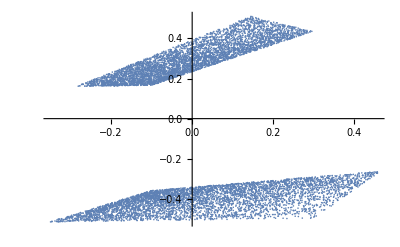

```mathematica
For[list={};i=0, i<NN, i++,
X = RandomReal[{-1,1}];
Y=RandomReal[{-1,1}];
Z=If[X>0,1,-1];
AppendTo[list,p[X,Y,Z]];
]
ListPlot[list]
```